```mathematica
q0=Exp[-(α+1)^2/2 x^2-(α(2α+1))/4 y^2+α(α+1)x y];
dq=(l+m x+n y+r x^2+s y^2+t x y)q0;
-α^2 D[(+x)q0,x]-α^2 D[(y-x)dq,x]+α/2(1-α/2 y^2)dq+D[dq,{y,2}]//Simplify;
%/q0//Simplify;
Collect[%//Expand,{x,y}]
```

2 s-α^2+y (-n α-m α^2-2 n α^2)+y^2 (-2 s α-4 s α^2-t α^2)+x^2 (2 t α+α^2+2 r α^2+2 t α^2+2 α^3+α^4)+x (2 n α+m α^2+2 n α^2+y (4 s α-t α-2 r α^2+4 s α^2-t α^2-α^3-α^4))

```mathematica
Solve[{2 s-α^2,
+(-n α-m α^2-2 n α^2),
+(-2 s α-4 s α^2-t α^2),
+(2 t α+α^2+2 r α^2+2 t α^2+2 α^3+α^4),
+(2 n α+m α^2+2 n α^2),
+(4 s α-t α-2 r α^2+4 s α^2-t α^2-α^3-α^4)}=={0,0,0,0,0,0},
{m,n,r,s,t}]//Simplify
```

{{m→0,n→0,r→1/2 (1+4 α+3 α^2),s→α^2/2,t→-α (1+2 α)}}

```mathematica
po=Exp[-(α+1)^2/2 x^2-(α(α+1))/2 y^2+α(α+1)x y];
pi=(1+1/2 (1+4 α+3 α^2)x^2+α^2/2 y^2-α (1+2 α)x y)po;
```

```mathematica
Assuming[α>0,Integrate[po,{y,-∞,∞}]]
Assuming[α>0,Integrate[pi,{y,-∞,∞}]]
%//Simplify
```

(ⅇ^(-1/2 x^2 (1+α)) √(2 π))/(√(α (1+α)))

(ⅇ^(-1/2 x^2 (1+α)) √(π/2) (2 √(α (1+α))+3 √(α^3 (1+α))+x^2 (√(α (1+α))+3 √(α^3 (1+α))+2 √(α^5 (1+α)))))/(α (1+α)^2)

(ⅇ^(-1/2 x^2 (1+α)) √(π/2) (2 √(α (1+α))+3 √(α^3 (1+α))+x^2 (√(α (1+α))+3 √(α^3 (1+α))+2 √(α^5 (1+α)))))/(α (1+α)^2)

```mathematica
Integrate[Exp[-1/2(a+1)x^2],{x,R,∞}]
```

ConditionalExpression[(√(π/2) Erfc[(√(1+a) R)/(√2)])/(√(1+a)),Re[a]>-1]

```mathematica
Assuming[a>0,Integrate[(2+3α+x^2(1+3α+2 α^2))Exp[-1/2(α+1)x^2],{x,X,∞}]]
```

ConditionalExpression[(ⅇ^(-1/2 X^2 (1+α)) (2 X √(1+α) (1+2 α)+ⅇ^(1/2 X^2 (1+α)) √(2 π) (3+5 α)-ⅇ^(1/2 X^2 (1+α)) √(2 π) (3+5 α) Erf[(X √(1+α))/(√2)]))/(2 √(1+α)),Re[α]>-1]

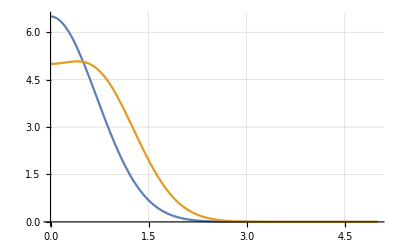

```mathematica
Plot[
{(2+3α+X^2(1+3α+2 α^2)),(2+3α+x^2(1+3α+2 α^2))}*Exp[-1/2(α+1)x^2]/.{X->0.5,α->1}//Evaluate,
{x,0,5},
GridLines->Automatic]
```

```mathematica
q0=Exp[-(α+1)^2/2 x^2-(α(2α+1))/4 y^2+α(α+1)x y];
dq=(l+m x+n y+r x^2+s y^2+t x y)q0;
-α^2 D[(ϵ x)q0,x]-α^2 D[(y-x)dq,x]+α/2(1-α/2 y^2)dq+D[dq,{y,2}]//Simplify;
%/q0//Simplify;
Collect[%//Expand,{x,y}]
Collect[%/.{s->α^2 ϵ/2,t->-α (1+2 α) ϵ,m->-n (1+2 α)/α}/.n->0//Simplify,{x,y}]
```

2 s+y (-n α-m α^2-2 n α^2)+y^2 (-2 s α-4 s α^2-t α^2)-α^2 ϵ+x^2 (2 t α+2 r α^2+2 t α^2+α^2 ϵ+2 α^3 ϵ+α^4 ϵ)+x (2 n α+m α^2+2 n α^2+y (4 s α-t α-2 r α^2+4 s α^2-t α^2-α^3 ϵ-α^4 ϵ))

-x^2 α^2 (-2 r+ϵ+4 α ϵ+3 α^2 ϵ)+x y α^2 (-2 r+ϵ+4 α ϵ+3 α^2 ϵ)

```mathematica
po=Exp[-(α+1)^2/2 x^2-(α(α+1))/2 y^2+α(α+1)x y];
pi=(1+ϵ 1/2 (1+4 α+3 α^2)x^2+ϵ α^2/2 y^2-ϵ α (1+2 α)x y)po;
pox=Assuming[α>0&&ϵ≥0,Integrate[po,{y,-∞,∞}]]//Simplify
pix=Assuming[α>0&&ϵ≥0,Integrate[pi,{y,-∞,∞}]]//Simplify
```

(ⅇ^(-1/2 x^2 (1+α)) √(2 π))/(√(α (1+α)))

(ⅇ^(-1/2 x^2 (1+α)) √(π/2) (2 (√(α (1+α))+√(α^3 (1+α)))+√(α^3 (1+α)) ϵ+x^2 (√(α (1+α))+3 √(α^3 (1+α))+2 √(α^5 (1+α))) ϵ))/(α (1+α)^2)

```mathematica
pix/pox//Simplify
1+(ϵ(a+x^2 (1+3a+2 a^2)))/(2 (1+a))
```

(α (2 (√(α (1+α))+√(α^3 (1+α)))+√(α^3 (1+α)) ϵ+x^2 (√(α (1+α))+3 √(α^3 (1+α))+2 √(α^5 (1+α))) ϵ))/(2 (α (1+α))^(3/2))

1+((a+(1+3 a+2 a^2) x^2) ϵ)/(2 (1+a))

```mathematica
Assuming[α>0,Integrate[√((α+1)/(2π))ⅇ^(-1/2 x^2 (1+α))x(aa x^2-1),{x,0,X}]]//Simplify
```

((-1+ⅇ^(-1/2 X^2 (1+α))) (1+α)+aa (2-ⅇ^(-1/2 X^2 (1+α)) (2+X^2 (1+α))))/(√(2 π) (1+α)^(3/2))

```mathematica
poxint=Assuming[α>0&&ϵ≥0&&X>0,Integrate[pox,{x,X,∞}]]//Simplify
pixint=Assuming[α>0&&ϵ≥0&&X>0,Integrate[pix,{x,0,X}]]//Simplify
```

(π Erfc[(X √(1+α))/(√2)])/(√α (1+α))

(ⅇ^(-1/2 X^2 (1+α)) (-√(2 π) X (1+3 α+2 α^2) ϵ+ⅇ^(1/2 X^2 (1+α)) π √(1+α) (2+ϵ+α (2+3 ϵ)) Erf[(X √(1+α))/(√2)]))/(2 √α (1+α)^(5/2))

```mathematica
(π Erfc[(X √(1+α))/(√2)])/(√α (1+α))
(π  Erf[(X √(1+α))/(√2)])/(√α (1+α))+ϵ((-√(2 π) X (1+3 α+2 α^2)ⅇ^(-1/2 X^2 (1+α)))/(2 √α (1+α)^(5/2))+(π  (1+3α ) Erf[(X √(1+α))/(√2)])/(2 √α (1+α)^2))
```

(π Erfc[(X √(1+α))/(√2)])/(√α (1+α))

(π Erf[(X √(1+α))/(√2)])/(√α (1+α))+ϵ (-(ⅇ^(-1/2 X^2 (1+α)) √(π/2) X (1+3 α+2 α^2))/(√α (1+α)^(5/2))+(π (1+3 α) Erf[(X √(1+α))/(√2)])/(2 √α (1+α)^2))

```mathematica
(1+ϵ(Erfc[√((α+1)/2)X] 1/(2(α+1))(α+(1+3α+2 α^2)X^2)+(1+3α)/(4(1+α))Erf[√((α+1)/2)X]-(X(1+3α+2 α^2)Exp[-1/2(α+1)X^2])/(4 √(π/2)(1+α)^(3/2))))-(1+ϵ 1/(2(α+1))((1+3α+2 α^2)(X^2 Erfc[√((α+1)/2)X]-√(2/π)(X Exp[-1/2(α+1)X^2])/(√(α+1)))+α+(1+2α)Erf[√((α+1)/2)X]))//Simplify
```

1/4 ϵ (-Erf[(X √(1+α))/(√2)]+(ⅇ^(-1/2 X^2 (1+α)) (-2 ⅇ^(1/2 X^2 (1+α)) α √(1+α)+√(2/π) X (1+3 α+2 α^2)+2 ⅇ^(1/2 X^2 (1+α)) α √(1+α) Erfc[(X √(1+α))/(√2)]))/(1+α)^(3/2))

```mathematica
(*B=1/(1+ϵ(Erfc[√((α+1)/2)X] 1/(2(α+1))(α+(1+3α+2 α^2)X^2)+(1+3α)/(4(1+α))Erf[√((α+1)/2)X]-(X(1+3α+2 α^2)Exp[-1/2(α+1)X^2])/(4 √(π/2)(1+α)^(3/2))));*)
B=1/(1+ϵ 1/(2(α+1))((1+3α+2 α^2)(X^2 Erfc[√((α+1)/2)X]-√(2/π)(X Exp[-1/2(α+1)X^2])/(√(α+1)))+α+(1+2α)Erf[√((α+1)/2)X]));
A=B(1+ϵ 1/(2(α+1))(α+(1+3α+2 α^2)X^2));
pout=A √((α+1)/(2π))Exp[-1/2(α+1)x^2];
pin=B(1+ϵ 1/(2(α+1))(α+(1+3α+2 α^2)x^2))√((α+1)/(2π))Exp[-1/2(α+1)x^2];
Manipulate[
Plot[
Piecewise[{{pout,x>X},{pin,x<X}}]/.{α->1,ϵ->ϵϵ,X->XX}//Evaluate,
{x,0,4},
PlotRange->All,Exclusions->None,
AxesLabel->{"x","p(x)"}],
{ϵϵ,0,1},{XX,0,1}]
```

#### Pressure

```mathematica
P=Assuming[α>0,
A √((α+1)/(2π))Integrate[x Exp[-1/2(α+1) x^2],{x,X,∞}]+
+B √((α+1)/(2π))(1-ϵ)Integrate[x Exp[-1/2(α+1) x^2](1+ϵ (α+(1+3α+2 α^2)x^2)/(2(α+1))),{x,0,X}]
]//Simplify
```

(-ⅇ^(1/2 X^2 (1+α)) (-1+ϵ) (2+2 α+2 ϵ+5 α ϵ)+ϵ ((2+X^2) ϵ+2 X^2 α^2 ϵ+α (-2+5 ϵ+3 X^2 ϵ)))/(√(2 π) (2 ⅇ^(1/2 X^2 (1+α)) √(1+α)+2 ⅇ^(1/2 X^2 (1+α)) α √(1+α)-√(2/π) X ϵ-3 √(2/π) X α ϵ-2 √(2/π) X α^2 ϵ+ⅇ^(1/2 X^2 (1+α)) α √(1+α) ϵ+ⅇ^(1/2 X^2 (1+α)) √(1+α) (1+2 α) ϵ Erf[(X √(1+α))/(√2)]+ⅇ^(1/2 X^2 (1+α)) X^2 √(1+α) (1+3 α+2 α^2) ϵ Erfc[(X √(1+α))/(√2)]))

```mathematica
Collect[Numerator[P],ϵ]
Collect[Denominator[P],ϵ]
```

2 ⅇ^(1/2 X^2 (1+α))+2 ⅇ^(1/2 X^2 (1+α)) α+(-2 α+3 ⅇ^(1/2 X^2 (1+α)) α) ϵ+(2-2 ⅇ^(1/2 X^2 (1+α))+X^2+5 α-5 ⅇ^(1/2 X^2 (1+α)) α+3 X^2 α+2 X^2 α^2) ϵ^2

√(2 π) (2 ⅇ^(1/2 X^2 (1+α)) √(1+α)+2 ⅇ^(1/2 X^2 (1+α)) α √(1+α))+√(2 π) ϵ (-√(2/π) X-3 √(2/π) X α-2 √(2/π) X α^2+ⅇ^(1/2 X^2 (1+α)) α √(1+α)+ⅇ^(1/2 X^2 (1+α)) √(1+α) (1+2 α) Erf[(X √(1+α))/(√2)]+ⅇ^(1/2 X^2 (1+α)) X^2 √(1+α) (1+3 α+2 α^2) Erfc[(X √(1+α))/(√2)])

```mathematica
Manipulate[
{A,B}/.X->XX/.α->αα/.ϵ->ϵϵ//Evaluate,
{αα,0,5},{ϵϵ,0,1},{XX,0,2}]
```

```mathematica
Manipulate[
Plot[{P,1/(√(2π(1+α)))}/.X->XX/.α->αα/.ϵ->ϵϵ//Evaluate,
{αα,0,5},
GridLines->Automatic,PlotRange->{All,{0,0.5}}],
{ϵϵ,0,1},{XX,0,2}]
```

```mathematica
Plot3D[
((1+3α+2 α^2)(X^2 Erfc[√((α+1)/2)X]-√(2/π)(X Exp[-1/2(α+1)X^2])/(√(α+1)))+α+(1+2α)Erf[√((α+1)/2)X]),
{α,0,10},{X,0,1}]
```

-Graphics3D-

```mathematica
NSolve[x^2==Exp[-x^2],{x}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.753089},{x→0.753089}}

#### 27/04/2016

```mathematica
p0=Exp[-(α+1)^2/2 x^2-(α(α+1))/2 y^2+α(α+1)x y];
dp=(l+m x+n y+r x^2+s y^2+t x y)p0;
-α^2 D[x p0,x]-α^2 D[(y-x)dp,x]+α D[y dp,y]+D[dp,{y,2}]//Simplify;
%/p0//Simplify;
pol=Collect[%//Expand,{x,y}]
```

2 s-α^2+y (-n α-m α^2-2 n α^2)+y^2 (-2 s α-4 s α^2-t α^2)+x^2 (2 t α+α^2+2 r α^2+2 t α^2+2 α^3+α^4)+x (2 n α+m α^2+2 n α^2+y (4 s α-t α-2 r α^2+4 s α^2-t α^2-α^3-α^4))

```mathematica
Solve[{2 s-α^2,
+(-n α-m α^2-2 n α^2),
+(-2 s α-4 s α^2-t α^2),
+(2 t α+α^2+2 r α^2+2 t α^2+2 α^3+α^4),
+(2 n α+m α^2+2 n α^2),
+(4 s α-t α-2 r α^2+4 s α^2-t α^2-α^3-α^4)}=={0,0,0,0,0,0},
{m,n,r,s,t}]//Simplify
```

{{m→0,n→0,r→1/2 (1+4 α+3 α^2),s→α^2/2,t→-α (1+2 α)}}

```mathematica
q0=Exp[-(α+1)^2/2 x^2-(α(2α+1))/4 y^2+α(α+1)x y];
dq=q0*HermiteH[n,y]*an[x,y];
0-α^2 D[(y-x)dq,x]+α/2(1-α/2 y^2)dq+D[dq,{y,2}]//Simplify;
%/q0//Simplify
```

2 n a[x,y,n] (2 (-1+n) HermiteH[-2+n,y]+α (2 x (1+α)-y (1+2 α)) HermiteH[-1+n,y])+(4 n HermiteH[-1+n,y]+α (2 x (1+α)-y (1+2 α)) HermiteH[n,y]) a^(0,1,0)[x,y,n]+HermiteH[n,y] (a^(0,2,0)[x,y,n]+(x-y) α^2 a^(1,0,0)[x,y,n])